# SFF

## Definiciones y paquetes

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\SFF

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\MG files\\SFF\\QMB.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
(*Needs["QMB`"]*)
```

```mathematica
ClearAll[ParityBH]
ParityBH[v_,n_,L_]:=Module[{basis=FockBasis[n,L],dic,neworder},
dic=AssociationThread[#->Range[Length[#]]]&[basis];
neworder=dic[Permute[#,Reverse[Range[Length[#]]]]]&/@basis;
v[[neworder]]
]
```

```mathematica
IndicesAfterParityBH[n_,L_]:=
Module[
{basis=FockBasis[n,L],dic,neworder},
dic=AssociationThread[#->Range[Length[#]]]&[basis];
dic[Permute[#,Reverse[Range[Length[#]]]]]&/@basis
]
```

```mathematica
ParityBH[v_,indexList_]:=v[[indexList]]
```

```mathematica
SFF[energies_,t_]:=Abs[Total[Exp[-I*energies*t]]]^2;
```

```mathematica
(*GOE prediction for spectral form factor*)
ClearAll[GOESFF]
GOESFF[t_]:=If[t<1,2t-t*Log[1+2*t],2-t*Log[(2t+1)/(2t-1)]]
```

#### Ejemplo ParityBH

```mathematica
n=L=2;
basis=FockBasis[n,L]
ParityBH[{1,0,0},n,L]
```

{{2,0},{1,1},{0,2}}

{0,0,1}

```mathematica
n=L=2;indexList=IndicesAfterParityBH[n,L];
basis=FockBasis[n,L]
ParityBH[{1,0,0},indexList]
```

{{2,0},{1,1},{0,2}}

{0,0,1}

## Fuzzy measurements model

```mathematica
n=L=6;
J=U=1.;(*chaotic regime*)
```

```mathematica
H=BoseHubbardHamiltonian[n,L,J,U];
{energies,eigenvecs}=Chop@Eigensystem[Normal@H];
```

```mathematica
(*from eigenvces, select those with positive parity*)
Module[{parity,indexList=IndicesAfterParityBH[n,L],pos},
parity=1.;
pos=Catenate[Position[Round[Braket[#,ParityBH[#,indexList]]&/@eigenvecs,1.],parity]];
symeigenvecs=eigenvecs[[pos]];
]
```

```mathematica
energies=Chop[Braket[#,H.#]&/@symeigenvecs];
energiesSHS=Chop[Module[{S=SwapMatrix[1,2,n,L]},Braket[#,S.H.S.#]&/@symeigenvecs]];
```

```mathematica
p=1.;(*probability of measuring correctly*)
fuzzyenergies=Sort[p*energies+(1-p)*energiesSHS];
(*s=#/Mean[#]&[Differences[fuzzyenergies[[500;;-500]]]];*)
(*we get rid of the tails of fuzzyspectrum and do a simple unfolding*)
unfoldedfuzzyenergies=Unfold[fuzzyenergies]["UnfoldedLevels"];
```

```mathematica
tH=2.Pi;f=1/25.
sffdata=Table[{(i+f),Mean[Chop[SFF[unfoldedfuzzyenergies,tH*#]]&/@Range[i,i+f,f/100]]/Length[energies]},{i,f,5.,f}];
```

0.04

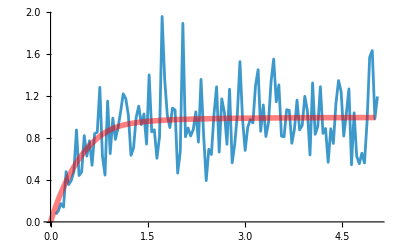

```mathematica
Show[
ListPlot[sffdata,Joined->True],
Plot[GOESFF[t],{t,0,5},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.5]],PlotRange->All]
]
```

```mathematica
p=0.9;(*probability of measuring correctly*)
fuzzyenergies=Sort[p*energies+(1-p)*energiesSHS];
(*s=#/Mean[#]&[Differences[fuzzyenergies[[500;;-500]]]];*)
(*we get rid of the tails of fuzzyspectrum and do a simple unfolding*)
unfoldedfuzzyenergies=Unfold[fuzzyenergies]["UnfoldedLevels"];
```

```mathematica
tH=2.Pi;f=1/25.
sffdata=Table[{(i+f),Mean[Chop[SFF[unfoldedfuzzyenergies,tH*#]]&/@Range[i,i+f,f/100]]/Length[energies]},{i,f,5.,f}];
```

0.04

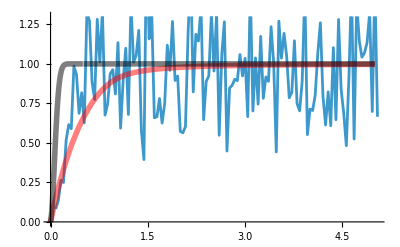

```mathematica
σ=10.;
Show[
ListPlot[sffdata,Joined->True,PlotRange->{All,{0,1.3}}],
Plot[GOESFF[t],{t,0,5},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.5]],PlotRange->All],
Plot[1+Exp[-σ^2 t^2](GOESFF[t]-1),{t,0,5},PlotStyle->Directive[Black,Thickness[0.01],Opacity[0.5]],PlotRange->All]
]
```